# BinaryTrees 1.04

## documentation notebook

Eric Rowland
https://ericrowland.github.io/packages.html

## Introduction

BinaryTrees is a package for generating, visualizing, and manipulating binary trees.
This introduction gets you started with a few features of the package; the next section provides a complete list of package symbols along with their usage messages and further examples.

To use BinaryTrees, first you will need to load the package by evaluating the following cell.  (If you need help, see loading a package.)

```mathematica
<<BinaryTrees`
```

### Representing trees

A rooted, ordered tree is represented by an expression in which each vertex corresponds to a list containing its children.  For example, here is a 5-leaf binary tree:

```mathematica
{{{},{}},{{{},{}},{}}}
```

The Wolfram Language symbol TreeForm displays expressions graphically.  BareTreeForm uses TreeForm to draw trees without vertex labels:

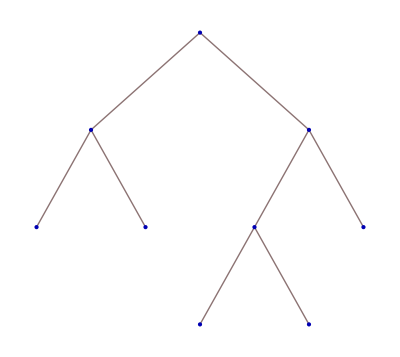

```mathematica
BareTreeForm[{{{},{}},{{{},{}},{}}}]
```

BinaryTrees gives a list of all binary trees with a fixed number of leaves.

{{{},{{},{{},{}}}},{{},{{{},{}},{}}},{{{},{}},{{},{}}},{{{},{{},{}}},{}},{{{{},{}},{}},{}}}

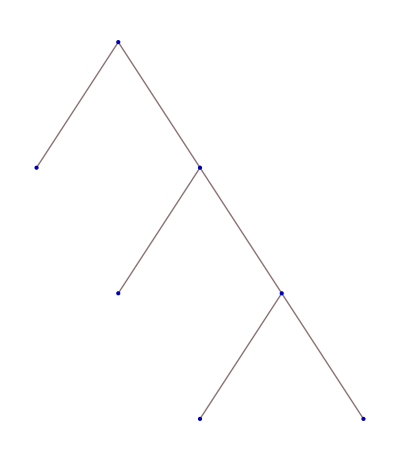
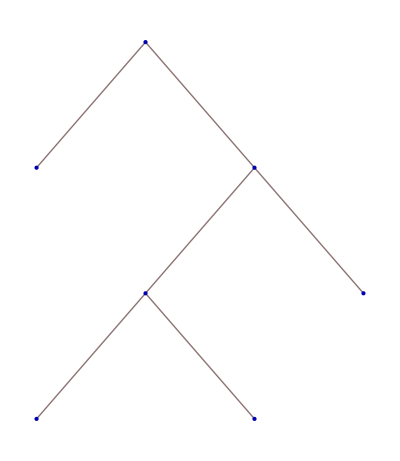
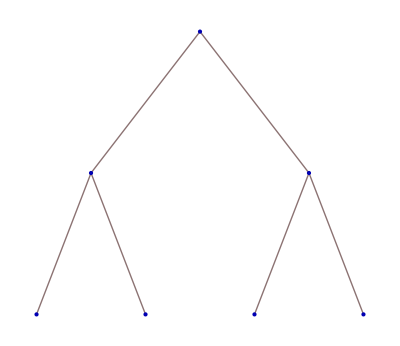
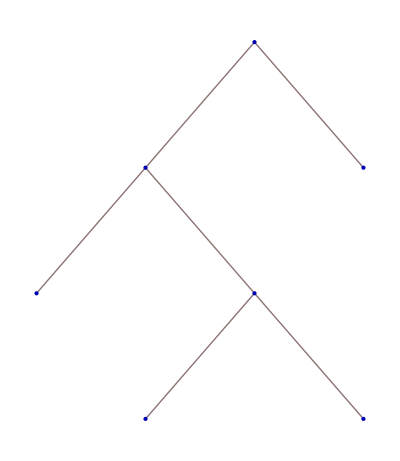
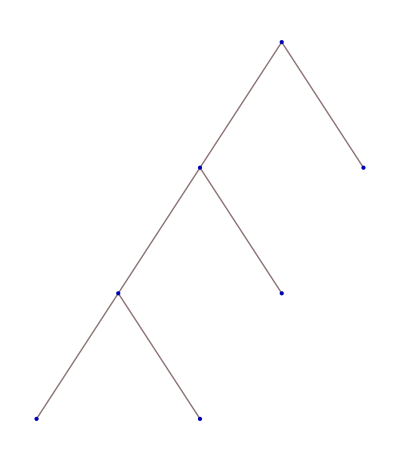

```mathematica
BinaryTrees[4]
BareTreeForm/@%
```

Trees gives a list of all trees with a fixed number of vertices.

{{{{{}}}},{{{},{}}},{{},{{}}},{{{}},{}},{{},{},{}}}

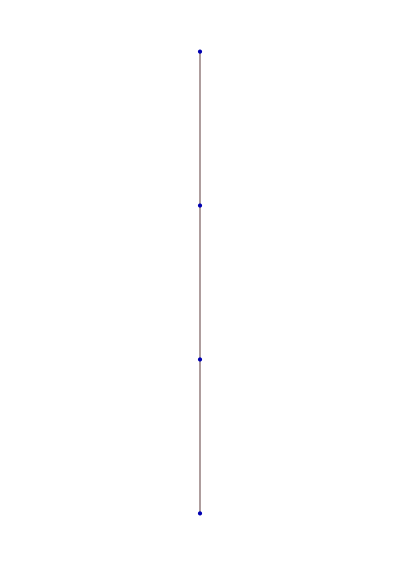
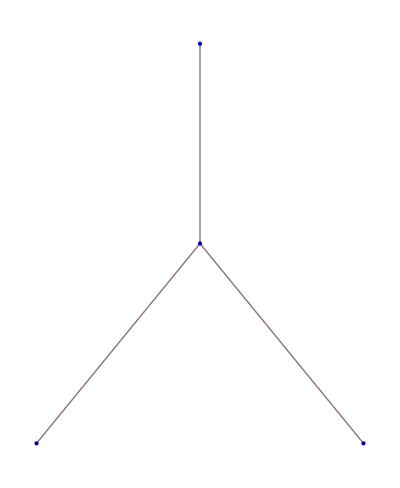
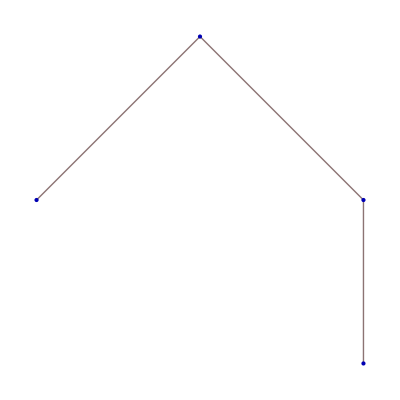
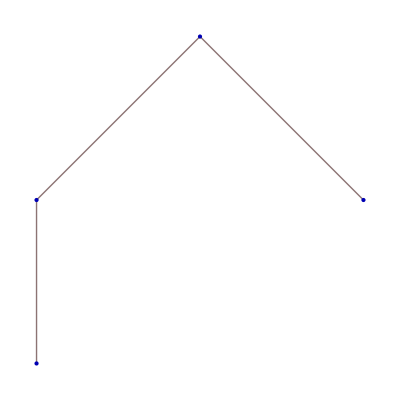
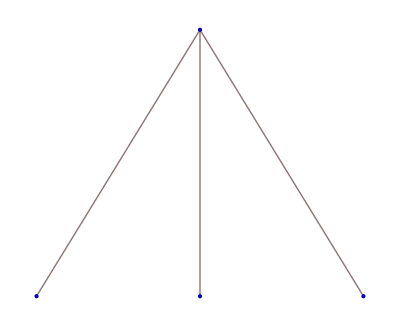

```mathematica
Trees[4]
BareTreeForm/@%
```

Rooted binary trees with n leaves are in bijection to general rooted trees with n vertices, via BinaryTree and its inverse, FromBinaryTree.

```mathematica
BareTreeForm/@BinaryTree/@Trees[4]
BareTreeForm/@FromBinaryTree/@BinaryTrees[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Trees with n vertices are also in bijection to Dyck words of length 2(n-1):

```mathematica
DyckWord/@Trees[4]
BareTreeForm/@FromDyckWord/@DyckWords[3]
```

{000111,001011,010011,001101,010101}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Families of trees

Several particular families of trees are implemented.

A path tree is a binary tree in which at most one vertex on each level has children of its own.  PathTrees gives the n-leaf path trees:

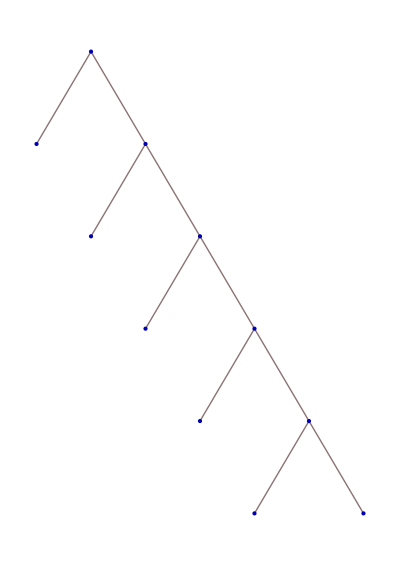
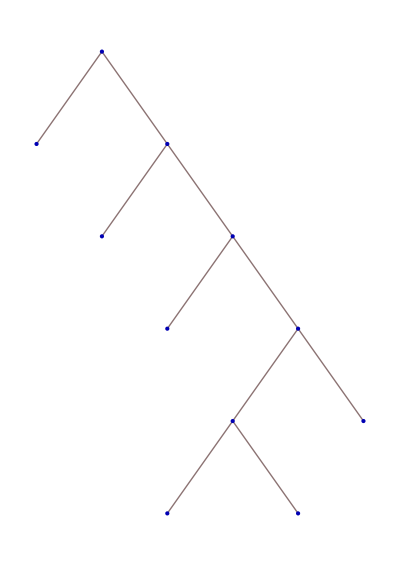
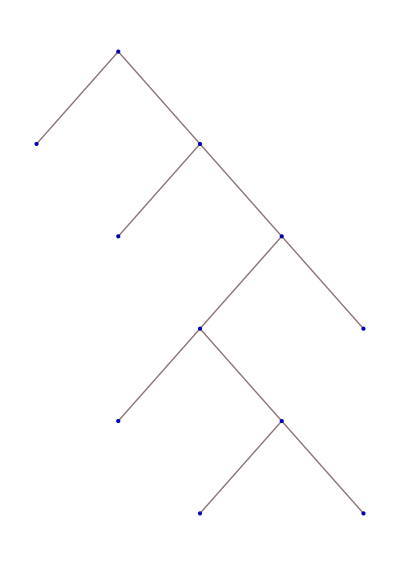
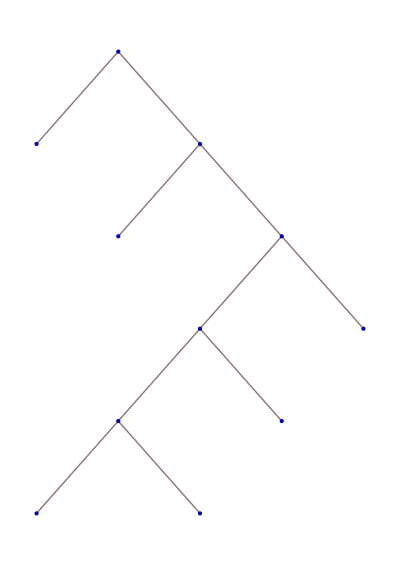
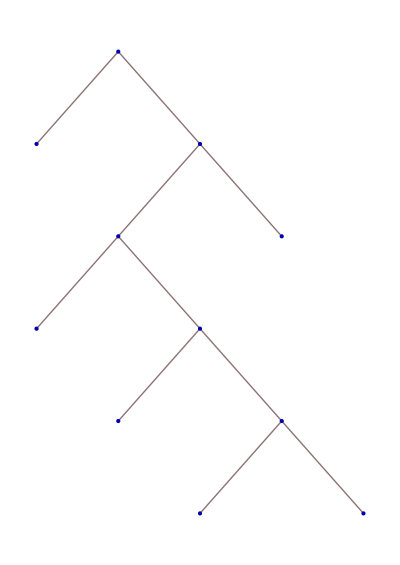
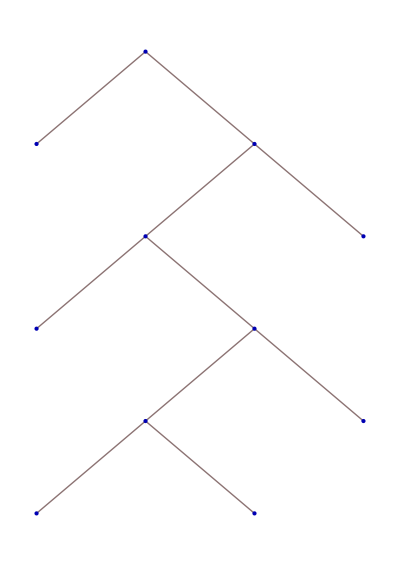
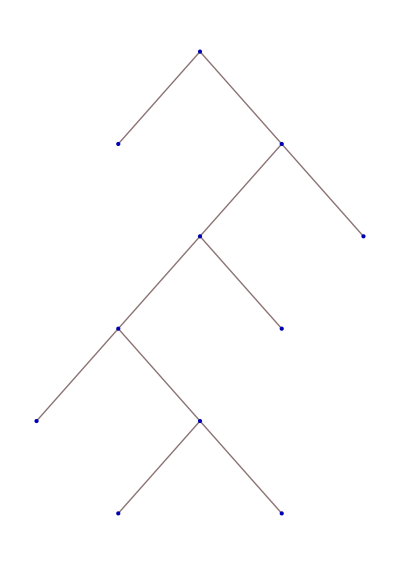
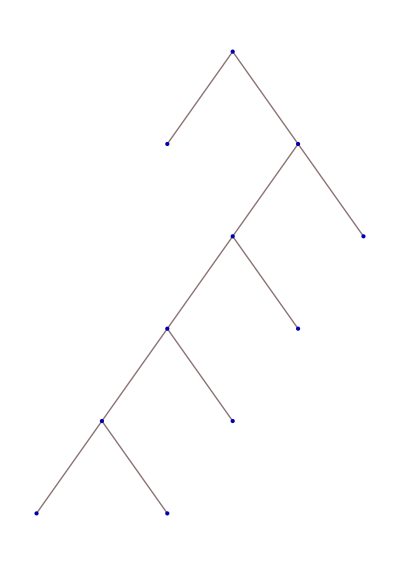

```mathematica
BareTreeForm/@PathTrees[6]
```

Since at each step we have the choice of the left vertex or right vertex having children, there are 2^(n-2) n-leaf path trees, and we can encode a path tree as a binary (n-2)-tuple.  PathTree constructs a path tree from a list of zeros and ones.

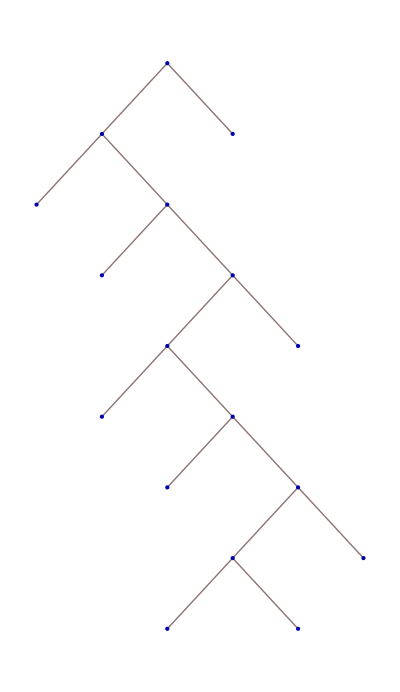

```mathematica
BareTreeForm[PathTree[{0,1,1,0,1,1,0}]]
```

FromPathTree constructs the binary tuple encoding a path tree.

```mathematica
FromPathTree[First[PathTrees[10]]]
```

{1,1,1,1,1,1,1,1}

The left comb tree is the path tree corresponding to {0,0,…,0}; the right comb tree is the path tree corresponding to {1,1,…,1}.

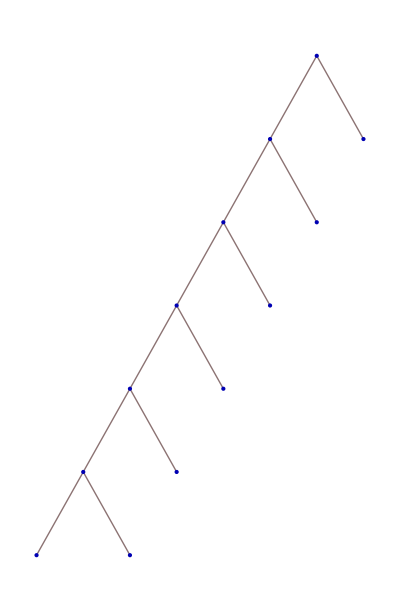

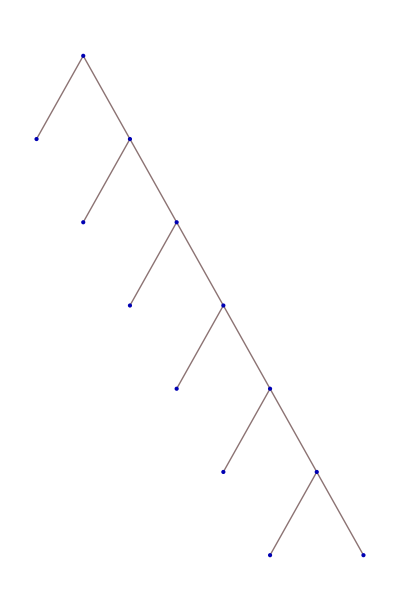

```mathematica
BareTreeForm[LeftCombTree[7]]
BareTreeForm[RightCombTree[7]]
```

LeftCrookedTree and RightCrookedTree give trees that alternate on each level.

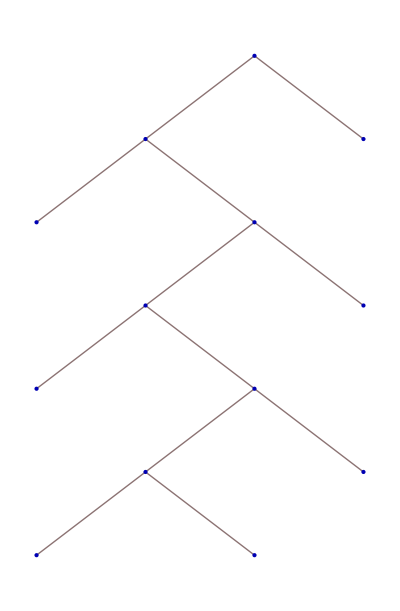

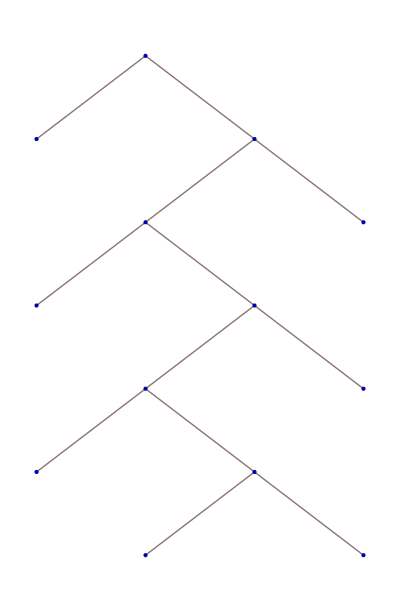

```mathematica
BareTreeForm[LeftCrookedTree[7]]
BareTreeForm[RightCrookedTree[7]]
```

## Package symbols

#### BareTreeForm

```mathematica
?BareTreeForm
```

RowBox[List["BareTreeForm", "[", StyleBox["expr", "TI"], "]"]] displays StyleBox["expr", "TI"] as an unlabeled tree with coloring to indicate instances of __ and ___.

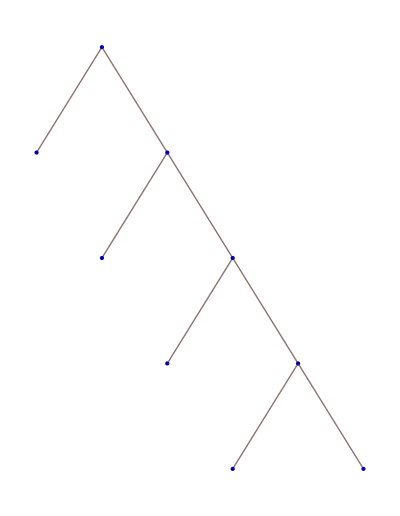
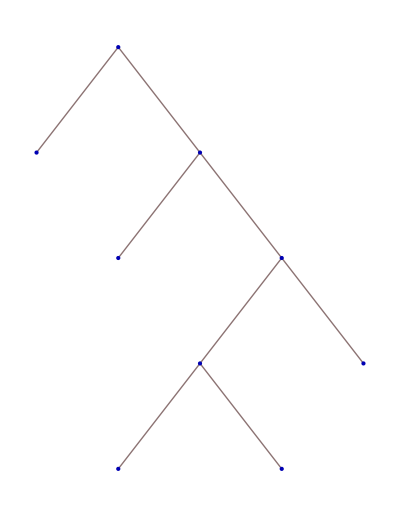
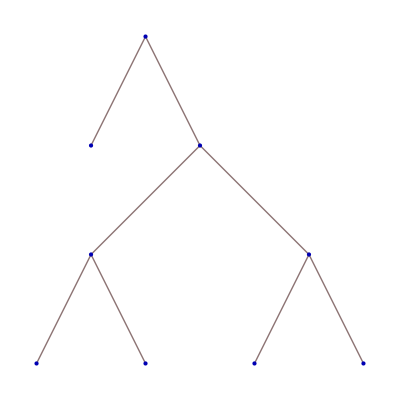
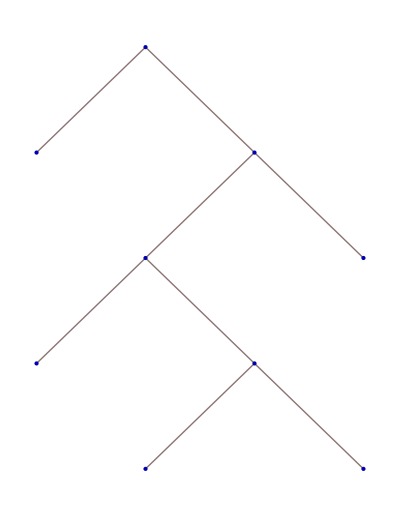
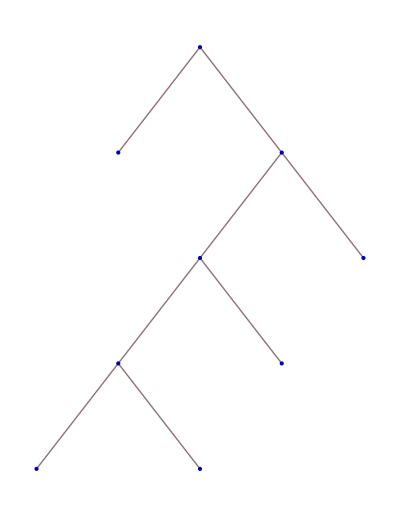
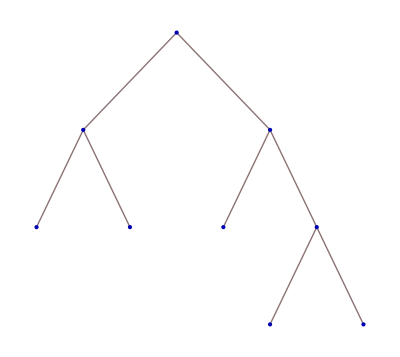
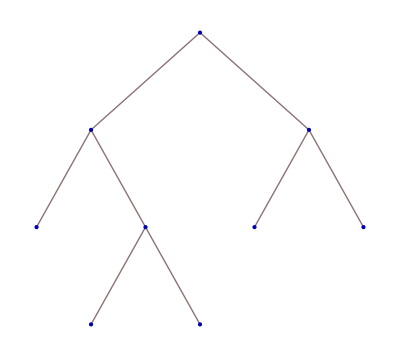
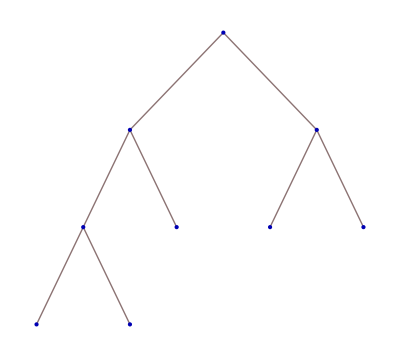
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BareTreeForm/@BinaryTrees[5]
```

The option LevelHeight can be used to adjust the size.

```mathematica
(BareTreeForm[#1,LevelHeight->20]&)/@BinaryTrees[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### BinaryTree and FromBinaryTree

```mathematica
?BinaryTree
```

RowBox[List["BinaryTree", "[", StyleBox["tree", "TI"], "]"]] gives the binary tree corresponding to a tree.

```mathematica
BinaryTree[Trees[5]⟦1⟧]
```

{{{{{},{}},{}},{}},{}}

```mathematica
?FromBinaryTree
```

RowBox[List["FromBinaryTree", "[", StyleBox["binarytree", "TI"], "]"]] gives the tree corresponding to a binary tree.

```mathematica
FromBinaryTree[BinaryTrees[5]⟦1⟧]
```

{{},{},{},{}}

#### BinaryTreeQ

```mathematica
?BinaryTreeQ
```

RowBox[List["BinaryTreeQ", "[", StyleBox["expr", "TI"], "]"]] yields True if StyleBox["expr", "TI"] is a binary tree, and False otherwise.

```mathematica
BinaryTreeQ[{{},{}}]
```

True

{{{},{{},{}}},{{{},{}},{}}}

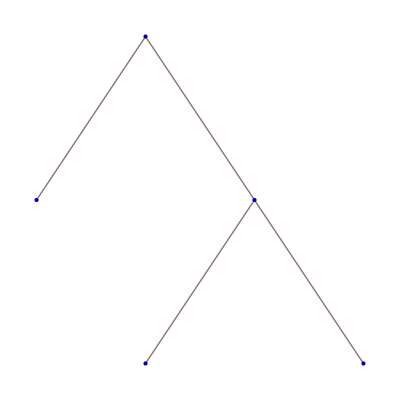
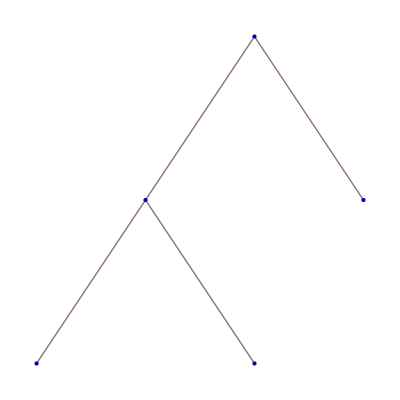

```mathematica
Select[Trees[5],BinaryTreeQ]
BareTreeForm/@%
```

#### BinaryTrees

```mathematica
?BinaryTrees
```

RowBox[List["BinaryTrees", "[", StyleBox["n", "TI"], "]"]] gives a list of all binary trees with StyleBox["n", "TI"] leaves.

```mathematica
BareTreeForm/@BinaryTrees[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### CompleteBinaryTree

```mathematica
?CompleteBinaryTree
```

RowBox[List["CompleteBinaryTree", "[", SuperscriptBox[StyleBox["2", "TR"], StyleBox["n", "TI"]], "]"]] gives the binary tree with SuperscriptBox[StyleBox["2", "TR"], StyleBox["n", "TI"]] leaves, all on the lowest level.

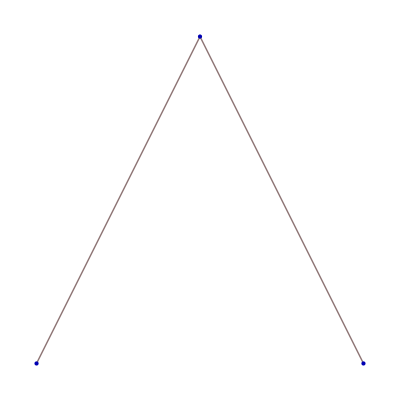
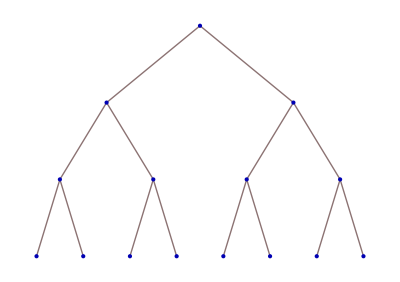
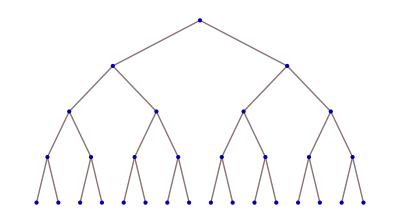
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[BareTreeForm[CompleteBinaryTree[2^n]],{n,0,4}]
```

#### DyckWord and FromDyckWord

```mathematica
?DyckWord
```

RowBox[List["DyckWord", "[", StyleBox["tree", "TI"], "]"]] gives the Dyck word corresponding to a tree.

```mathematica
DyckWord/@Trees[5]
```

{00001111,00010111,00100111,00011011,00101011,01000111,01001011,00110011,00011101,00101101,01010011,01001101,00110101,01010101}

```mathematica
?FromDyckWord
```

RowBox[List["FromDyckWord", "[", StyleBox["word", "TI"], "]"]] gives the tree corresponding to a Dyck word.

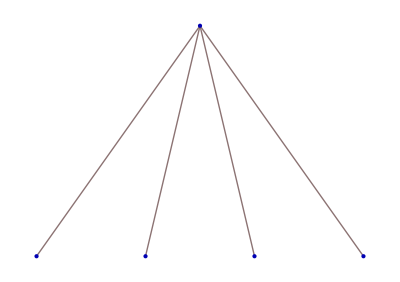
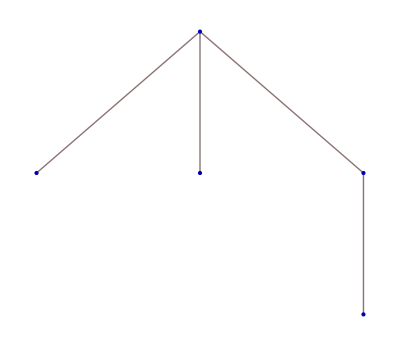
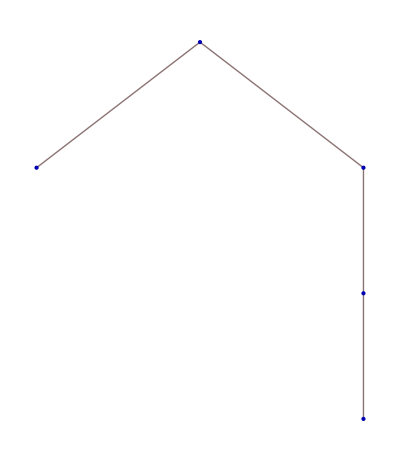
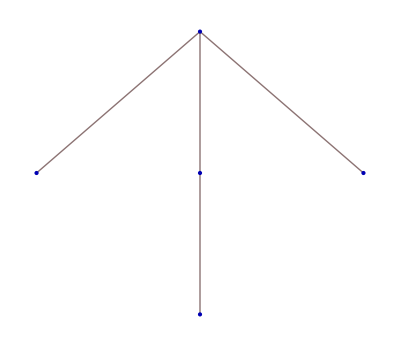
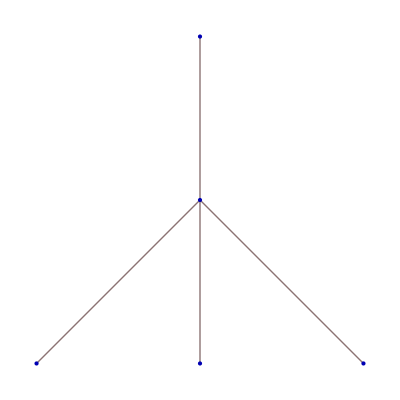
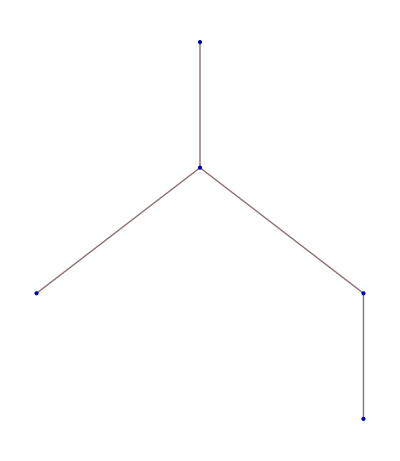
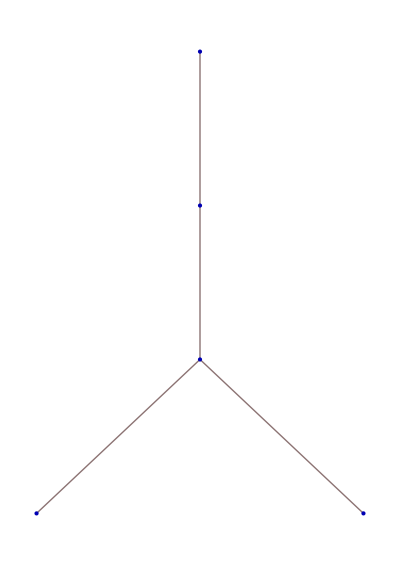
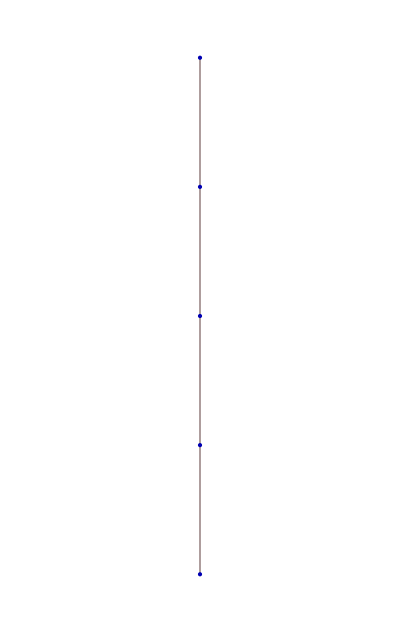
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BareTreeForm/@FromDyckWord/@DyckWords[4]
```

#### DyckWordQ

```mathematica
?DyckWordQ
```

RowBox[List["DyckWordQ", "[", StyleBox["string", "TI"], "]"]] yields True if StyleBox["string", "TI"] is a Dyck word on {"0", "1"}, and False otherwise.

```mathematica
DyckWordQ["0110"]
```

False

```mathematica
DyckWordQ["0101"]
```

True

#### DyckWords

```mathematica
?DyckWords
```

RowBox[List["DyckWords", "[", StyleBox["n", "TI"], "]"]] gives a list of the length-RowBox[List[StyleBox["2", "TR"], " ", StyleBox["n", "TI"]]] Dyck words on {"0", "1"}.

```mathematica
DyckWords[4]
```

{01010101,01010011,01001011,01000111,01001101,00101011,00100111,00010111,00001111,00011011,00110101,00110011,00101101,00011101}

#### LeftCombTree and RightCombTree

```mathematica
?LeftCombTree
```

RowBox[List["LeftCombTree", "[", StyleBox["n", "TI"], "]"]] gives the StyleBox["n", "TI"]-leaf path tree in which only the left child of a vertex has children.

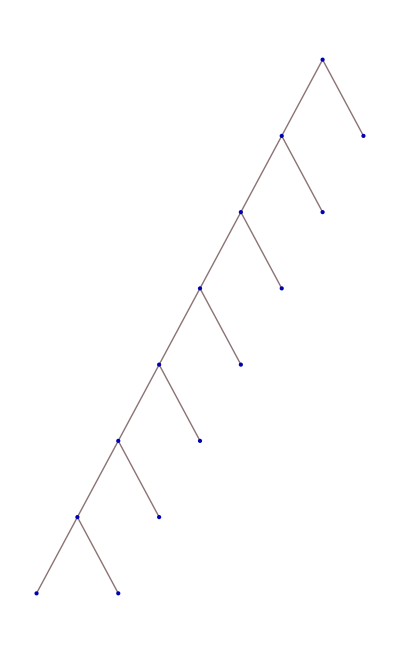
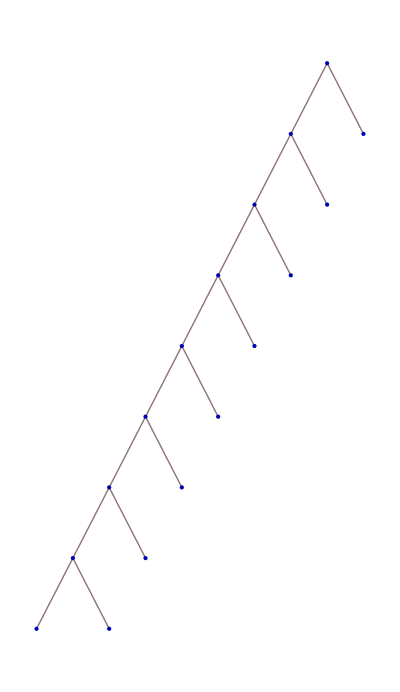
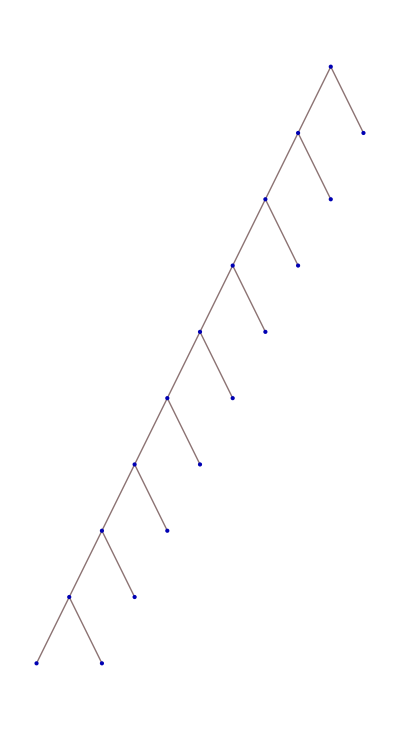
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BareTreeForm/@LeftCombTree/@Range[10]
```

```mathematica
?RightCombTree
```

RowBox[List["RightCombTree", "[", StyleBox["n", "TI"], "]"]] gives the StyleBox["n", "TI"]-leaf path tree in which only the right child of a vertex has children.

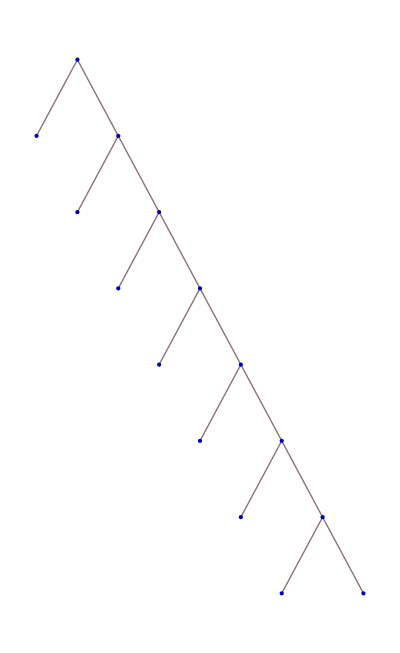
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BareTreeForm/@RightCombTree/@Range[10]
```

#### LeftCrookedTree and RightCrookedTree

```mathematica
?LeftCrookedTree
```

RowBox[List["LeftCrookedTree", "[", StyleBox["n", "TI"], "]"]] gives the StyleBox["n", "TI"]-leaf path tree in which alternate vertices on successive levels have children, beginning with the left child.

```mathematica
BareTreeForm/@LeftCrookedTree/@Range[2,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?RightCrookedTree
```

RowBox[List["RightCrookedTree", "[", StyleBox["n", "TI"], "]"]] gives the StyleBox["n", "TI"]-leaf path tree in which alternate vertices on successive levels have children, beginning with the right child.

```mathematica
BareTreeForm/@RightCrookedTree/@Range[2,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### LeftPathTree and RightPathTree

```mathematica
?LeftPathTree
```

RowBox[List["LeftPathTree", "[", RowBox[List[SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["\[Ellipsis]", "TR"], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["k", "TI"]]]], "]"]] gives the (RowBox[List[SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], "+", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], "+", StyleBox["\[CenterEllipsis]", "TR"], "+", SubscriptBox[StyleBox["n", "TI"], StyleBox["k", "TI"]]]])-leaf path tree made up of combs of length SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]], beginning with a left comb.

```mathematica
?RightPathTree
```

RowBox[List["RightPathTree", "[", RowBox[List[SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["\[Ellipsis]", "TR"], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["k", "TI"]]]], "]"]] gives the (RowBox[List[SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], "+", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], "+", StyleBox["\[CenterEllipsis]", "TR"], "+", SubscriptBox[StyleBox["n", "TI"], StyleBox["k", "TI"]]]])-leaf path tree made up of combs of length SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]], beginning with a right comb.

```mathematica
Row[Table[BareTreeForm[LeftPathTree@@Range[n]],{n,2,10}]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### LeftTurnTree and RightTurnTree

```mathematica
?LeftTurnTree
```

RowBox[List["LeftTurnTree", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]] gives the (RowBox[List[StyleBox["n", "TI"], "+", StyleBox["m", "TI"]]])-leaf path tree made up of an (RowBox[List[StyleBox["n", "TI"], "+", StyleBox["1", "TR"]]])-leaf left comb and an StyleBox["m", "TI"]-leaf right comb.

```mathematica
?RightTurnTree
```

RowBox[List["RightTurnTree", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]] gives the (RowBox[List[StyleBox["n", "TI"], "+", StyleBox["m", "TI"]]])-leaf path tree made up of an (RowBox[List[StyleBox["n", "TI"], "+", StyleBox["1", "TR"]]])-leaf right comb and an StyleBox["m", "TI"]-leaf left comb.

```mathematica
BareTreeForm[LeftTurnTree[2,3]]
```

-Graphics-

```mathematica
Grid[Table[BareTreeForm[LeftTurnTree[m,n]],{m,4},{n,2,7}]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### PathTree and FromPathTree

```mathematica
?PathTree
```

RowBox[List["PathTree", "[", StyleBox["tuple", "TI"], "]"]] gives the path tree corresponding to a RowBox[List["{", RowBox[List[StyleBox["0", "TR"], ",", StyleBox["1", "TR"]]], "}"]]-tuple.

‘0’ means ‘left’, and ‘1’ means ‘right’:

```mathematica
BareTreeForm[PathTree[{0,0,0,0,0,0,0}]]
```

-Graphics-

```mathematica
?FromPathTree
```

RowBox[List["FromPathTree", "[", StyleBox["pathtree", "TI"], "]"]] gives the RowBox[List["{", RowBox[List[StyleBox["0", "TR"], ",", StyleBox["1", "TR"]]], "}"]]-tuple corresponding to a path tree.

```mathematica
FromPathTree/@PathTrees[5]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

#### PathTreeQ

```mathematica
?PathTreeQ
```

RowBox[List["PathTreeQ", "[", StyleBox["expr", "TI"], "]"]] yields True if StyleBox["expr", "TI"] is a path tree, and False otherwise.

```mathematica
BareTreeForm/@Select[BinaryTrees[5],PathTreeQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### PathTrees

```mathematica
?PathTrees
```

RowBox[List["PathTrees", "[", StyleBox["n", "TI"], "]"]] gives a list of all path trees with StyleBox["n", "TI"] leaves.

```mathematica
BareTreeForm/@PathTrees[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### RandomBinaryTree

```mathematica
?RandomBinaryTree
```

RowBox[List["RandomBinaryTree", "[", StyleBox["n", "TI"], "]"]] gives a pseudorandom binary tree with StyleBox["n", "TI"] leaves.

```mathematica
Table[BareTreeForm[RandomBinaryTree[20]],{10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### RandomPathTree

```mathematica
?RandomPathTree
```

RowBox[List["RandomPathTree", "[", StyleBox["n", "TI"], "]"]] gives a pseudorandom path tree with StyleBox["n", "TI"] leaves.

```mathematica
Table[BareTreeForm[RandomPathTree[20]],{10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### RankBinaryTree

```mathematica
?RankBinaryTree
```

RowBox[List["RankBinaryTree", "[", StyleBox["tree", "TI"], "]"]] gives the position of an StyleBox["n", "TI"]-leaf binary tree in RowBox[List["BinaryTrees", "[", StyleBox["n", "TI"], "]"]].

```mathematica
RankBinaryTree[{{},{{},{{{{},{}},{{{{},{}},{}},{}}},{}}}}]
```

109

```mathematica
BinaryTrees[9]⟦109⟧=={{},{{},{{{{},{}},{{{{},{}},{}},{}}},{}}}}
```

True

#### RankTree

```mathematica
?RankTree
```

RowBox[List["RankTree", "[", StyleBox["tree", "TI"], "]"]] gives the position of an StyleBox["n", "TI"]-vertex tree in RowBox[List["Trees", "[", StyleBox["n", "TI"], "]"]].

```mathematica
RankTree[{{{},{},{{},{},{{}}}}}]
```

275

```mathematica
Trees[9]⟦275⟧=={{{},{},{{},{},{{}}}}}
```

True

#### TreeChop

```mathematica
?TreeChop
```

RowBox[List["TreeChop", "[", RowBox[List[StyleBox["expr", "TI"], ",", StyleBox["d", "TI"]]], "]"]] replaces all subexpressions of StyleBox["expr", "TI"] at depth StyleBox["d", "TI"] with {}.

```mathematica
tree=CompleteBinaryTree[64];
```

```mathematica
BareTreeForm[tree]
```

-Graphics-

```mathematica
BareTreeForm[TreeChop[tree,3]]
```

-Graphics-

```mathematica
Clear[tree]
```

#### TreeEdgeRules and FromTreeEdgeRules

```mathematica
?TreeEdgeRules
```

RowBox[List["TreeEdgeRules", "[", StyleBox["tree", "TI"], "]"]] gives a list of parent-child relationships in a tree, where a vertex is represented by its position in the breadth-first traversal of the tree.

```mathematica
tree={{},{{{{{}}}},{{},{{}}}}};
BareTreeForm[tree]
```

-Graphics-

```mathematica
TreeEdgeRules[tree]
```

{1→2,1→3,3→4,3→5,4→6,5→7,5→8,6→9,8→10,9→11}

```mathematica
?FromTreeEdgeRules
```

RowBox[List["FromTreeEdgeRules", "[", StyleBox["rules", "TI"], "]"]] constructs a tree from its list of parent-child relationships, where a vertex is represented by its position in the breadth-first traversal of the tree.

```mathematica
FromTreeEdgeRules[{1->2,1->3,3->4,3->5,4->6,5->7,5->8,6->9,8->10,9->11}]
```

{{},{{{{{}}}},{{},{{}}}}}

```mathematica
Clear[tree]
```

#### Trees

```mathematica
?Trees
```

RowBox[List["Trees", "[", StyleBox["n", "TI"], "]"]] gives a list of all rooted trees with StyleBox["n", "TI"] vertices.
RowBox[List["Trees", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["degrees", "TI"]]], "]"]] gives a list of all rooted trees with StyleBox["n", "TI"] vertices such that the number of children of each vertex is a member of the list StyleBox["degrees", "TI"].

```mathematica
BareTreeForm/@Trees[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}